Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

5. CAS problem. Partial sums.
In example 1 in the text verify the values of A_0, A_1, A_2, A_3 and compute A_4, ⋯ , A_10. Try to find out graphically how well the corresponding partial sums of (23) approximate the given boundary function.

The text gives the helpful info that M=n/2 for even n; M=(n-1)/2 for odd n.

```mathematica
An=(55(2 n+1))/2^n Sum[(-1)^m((2n-2m )!)/(m!(n-m)!(n-2 m+1)!),{m,0,M}];
```

```mathematica
An0=(55(2 n+1))/2^n Sum[(-1)^m((2n-2m )!)/(m!(n-m)!(n-2 m+1)!),{m,0,0}]/.n->0
```

55

```mathematica
An1=(55(2 n+1))/2^n Sum[(-1)^m((2n-2m )!)/(m!(n-m)!(n-2 m+1)!),{m,0,0}]/.n->1
```

165/2

```mathematica
An2=(55(2 n+1))/2^n Sum[(-1)^m((2n-2m )!)/(m!(n-m)!(n-2 m+1)!),{m,0,1}]/.n->2
```

0

```mathematica
An3=(55(2 n+1))/2^n Sum[(-1)^m((2n-2m )!)/(m!(n-m)!(n-2 m+1)!),{m,0,1}]/.n->3
```

-385/8

```mathematica
An4=(55(2 n+1))/2^n Sum[(-1)^m((2n-2m )!)/(m!(n-m)!(n-2 m+1)!),{m,0,2}]/.n->4
```

0

```mathematica
An5=(55(2 n+1))/2^n Sum[(-1)^m((2n-2m )!)/(m!(n-m)!(n-2 m+1)!),{m,0,2}]/.n->5
```

605/16

```mathematica
An6=(55(2 n+1))/2^n Sum[(-1)^m((2n-2m )!)/(m!(n-m)!(n-2 m+1)!),{m,0,3}]/.n->6
```

0

```mathematica
An7=(55(2 n+1))/2^n Sum[(-1)^m((2n-2m )!)/(m!(n-m)!(n-2 m+1)!),{m,0,3}]/.n->7
```

-4125/128

```mathematica
An8=(55(2 n+1))/2^n Sum[(-1)^m((2n-2m )!)/(m!(n-m)!(n-2 m+1)!),{m,0,4}]/.n->8
```

0

```mathematica
An9=(55(2 n+1))/2^n Sum[(-1)^m((2n-2m )!)/(m!(n-m)!(n-2 m+1)!),{m,0,4}]/.n->9
```

7315/256

```mathematica
An10=(55(2 n+1))/2^n Sum[(-1)^m((2n-2m )!)/(m!(n-m)!(n-2 m+1)!),{m,0,5}]/.n->10
```

0

The green cells above match the text answer.

The boundary function is:

```mathematica
f[ϕ_]=Piecewise[{{110,0≤ϕ<π/2},{0,π/2<ϕ≤π}}]
```

Piecewise[{{110, 0≤ϕ<π/2}, {0, True}}]

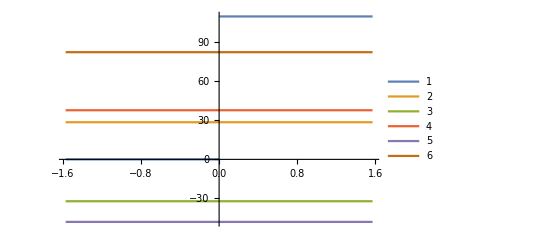

```mathematica
Plot[{{f[ϕ]},{An9},{An7},{An5},{An3},{An1}},{ϕ,-π/2,π/2},PlotLegends->Automatic]
```

An9=orange; An7=green; An5=red; An3=purple; An1=brown; f(ϕ)=teal

8 - 15 Potentials Depending only on r

9. Spherical symmetry. Show that the only solution of Laplace’s equation depending on r=√((x^2) + y^2 +z^2) is u=c/r+ k with constant c and k.

The s.m. solves this problem in spherical coordinates. Differentiation is applied, and perhaps the key discovery is a form equivalent to an Euler-Cauchy equation, numbered line (1) on p. 71. Equivalence to the proposed equation is established, but I did not notice arguments advanced for exclusivity. Maybe I missed some implied references.

13. Dirichlet problem. Find the electrostatic potential between two concentric spheres of radii r_1 =2 cm and r_2 = 4 cm kept at the potentials U_1=220 V and U_2=140 V, respectively. Sketch and compare the equipotential lines in problems 12 and 13.

```mathematica
Clear["Global`*"]
```

This probem is covered in the s.m. The s.m. notes that a spherically symmetric solution of the 3D Laplace equation is

u=u[r]=c/r+k  where c,k are constants, as has just been shown in problem 9.

The constants can be determined by the two boundary conditions u(2)=220 and u(4) =140.

```mathematica
Solve[c/2+k==220&&c/2+2 k==280,{c,k}]
```

{{c→320,k→60}}

making the solution

```mathematica
u[r]=320/r+60;
```

```mathematica
Clear["Global`*"]
```

The green cell above matches the text answer. As for the sketch, an attempt is made below:

```mathematica
scalarField2=x^2+y^2+z^2;
scalarField4=x^2+y^2+z^2;
vectorField=D[scalarField2,{{x,y,z}}]
```

{2 x,2 y,2 z}

```mathematica
c2=ContourPlot3D[scalarField2==2,{x,-2,2},{y,-2,2},{z,-2,2},Mesh->None,ContourStyle->Opacity[1.0,Green]];
c3=ContourPlot3D[scalarField4==4,{x,-2,0},{y,-2,2},{z,-2,2},Mesh->None,ContourStyle->Opacity[0.3,Red]];
v=VectorPlot3D[vectorField,{x,-2,2},{y,-2,2},{z,-2,2},VectorPoints->15,VectorScale->{0.1,Scaled[0.6]},RegionFunction->Function[{x,y,z},2.3≤scalarField2≤3.5]];
Show[c2,c3,v]
```

-Graphics3D-

The above plot is an attempt to make something that looks right, though it is not, really. I first restricted the domain of scalarfield2 to [-2,0], just like scalarfield4, so I could check to see where the normal arrows were emerging from (I wanted them to emerge from the surface of scalarfield2.) Using the value 2.3 for region function min had the roots of the arrows just barely showing through the skin of scalarfield2 (but it was totally a visual judgment.) Likewise, using 3.5 for region function max seemed to bring the arrows to the surface of scalarfield4, or close to it. It would be interesting to know the actual commands to use to get a realistic plot.

16 -20 Boundary Value Problems in Spherical Coordinates r, θ, ϕ
Find the potential in the interior of the sphere r = R = 1 if the interior is free of charges and the potential on the sphere is

17. f(ϕ)=1

```mathematica
Clear["Global`*"]
```

Since problem 19 is covered in the s.m., it was worked first. As in that problem, I suppose that the formula from numbered line (16a) on p. 596 is needed,
u_n[r_,ϕ_]=A_n r^n P_n Cos[ϕ]

Only the zeroth coefficient and the zeroth term of the Legendre polynomial is needed, I guess:

```mathematica
LegendreP[0,0,x]
```

1

The A_n coefficient, I believe, is 1. So the answer should be:

```mathematica
u[r_,ϕ_]=1 r^0 1 LegendreP[0,0,ϕ]
```

1

The above answer matches the answer in the text. I hope I did not put in too many 1s.

19. f(ϕ)=Cos[2 ϕ]

```mathematica
Clear["Global`*"]
```

This problem is covered in the s.m., and I don’t see a way for Mathematica to reduce the solution path. The narrative starts out with a reference to Fourier-Legendre series,

a_0 P_0+a_1 P_1+a_2 P_2+⋯ where P_0, P_1, P_2 are Legendre polynomials. The s.m. wants to use the

substitution w=Cos[ϕ]. In order to use Legendre polynomials, which involve powers of w, it will be necessary to transform the starting function Cos[2 ϕ] into powers of Cos[ϕ]. The s.m. pulls a trig identity from numbered line (10) of p. A-64,  cos^2 x=1/2(1+cos 2x), leading to Cos[2 θ]=2 Cos[θ]^2-1=2 w^2-1

With regard to Legendre polynomials, the s.m. notes that:

```mathematica
LegendreP[0,0,x]
```

1

```mathematica
LegendreP[1,0,x]
```

x

```mathematica
LegendreP[2,0,x]
```

1/2 (-1+3 x^2)

The s.m. states that, based on 2w^2-1, the Legendre polynomial powers of 0 and 2 will be needed (power 1 dropped). Introducing working coefficients A and B,

```mathematica
2 w^2-1==A LegendreP[0,0,w]+B LegendreP[2,0,w]
```

-1+2 w^2==A+1/2 B (-1+3 w^2)

```mathematica
Expand[%]
```

-1+2 w^2==A-B/2+(3 B w^2)/2

```mathematica
Solve[(3 B)/2==2,B]
```

{{B→4/3}}

```mathematica
Solve[-1==A-B/2,{A}]
```

{{A→1/2 (-2+B)}}

```mathematica
%/.B->4/3
```

{{A→-1/3}}

Folding A and B into the cyan cell above,

```mathematica
2 w^2-1==-1/3 LegendreP[0,0,w]+4/3 LegendreP[2,0,w];
```

The s.m. notes that numbered line (16a) on p. 596 is needed,
u_n[r_,ϕ_]=A_n r^n P_n Cos[ϕ]

As for what the yellow cell represents, it is the zeroth term and the 2nd term of the series just introduced, the first term having dropped out as noted above. Putting it in terms of u(r,ϕ),

```mathematica
u[r_,ϕ_] = -1/3 Subscript[P, 0] Cos[ϕ]+4/3 r^2 Subscript[P, 2] Cos[ϕ];
```

The above cell matches the answer in the s.m., with the notation P_n replacing the Mathematica LegendreP notation, and the value of P_0, which is 1, not yet substituted. As for the text answer, the term -1/3 P_0 Cos[ϕ] is given as simply -1/3, and so does not agree in this case with the s.m.